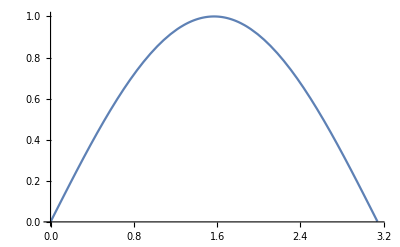

```mathematica
Plot[Sin[x],{x,0,3.14}]
```

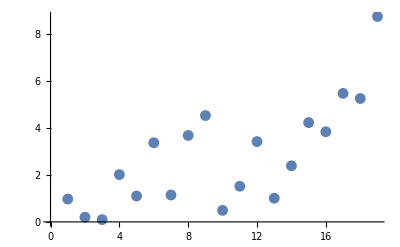

```mathematica
ListPlot[Table[RandomReal[x],{x,1,10,0.5}]]
```

```mathematica
ListLinePlot[Table[RandomReal[x],{x,1,10,0.5}]]
```

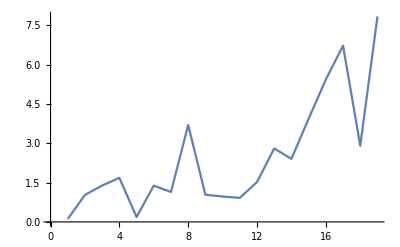

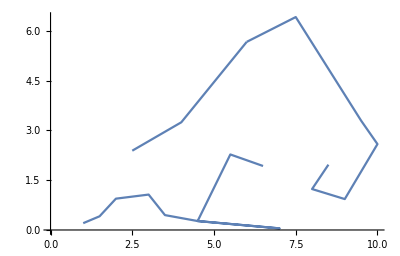

```mathematica
ListCurvePathPlot[Table[{x,RandomReal[x]},{x,1,10,0.5}]]
```

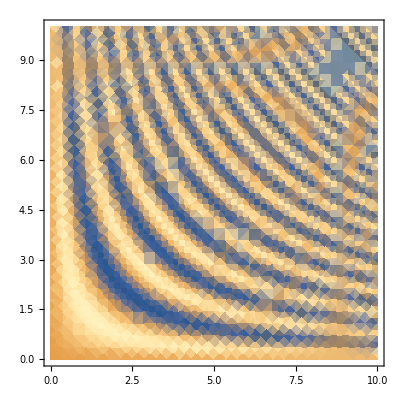

```mathematica
DensityPlot[Sin[x*y],{x,0,10},{y,0,10}]
```

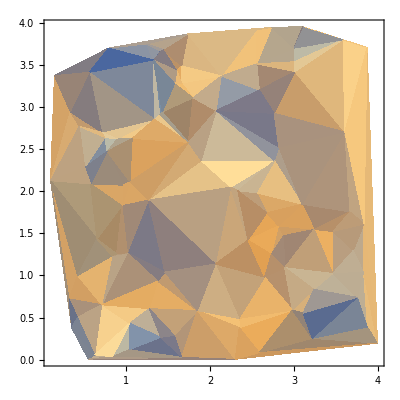

```mathematica
ListDensityPlot[RandomReal[{0,4},{100,3}]]
```

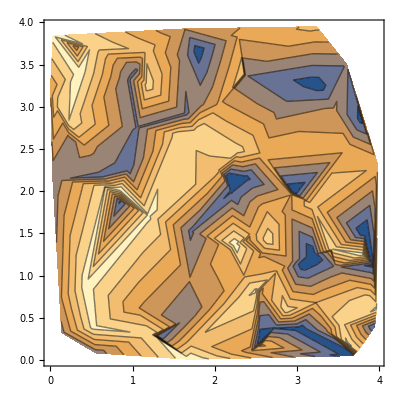

```mathematica
ListContourPlot[RandomReal[{0,4},{100,3}]]
```

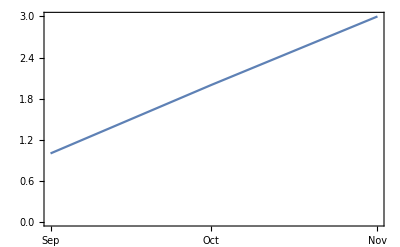

```mathematica
DateListPlot[{1,2,3},{2008,9}]
```

```mathematica
ParametricPlot3D[{Sin[t],Cos[t],t/3},{t,0,15}]
```

-Graphics3D-

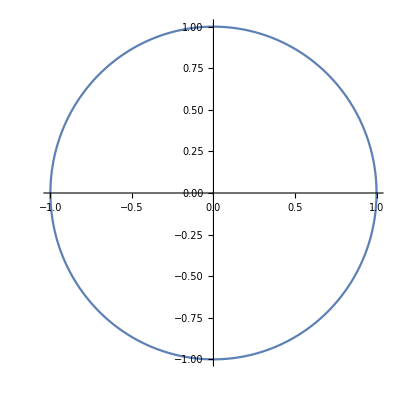

```mathematica
ParametricPlot[{Sin[t],Cos[t]},{t,0,2Pi}]
```

```mathematica
Needs["StatisticalPlots`"]
```

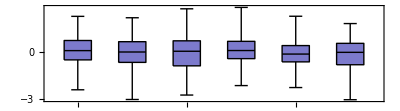

```mathematica
BoxWhiskerPlot[RandomReal[NormalDistribution[0,1],{100,6}]]
```

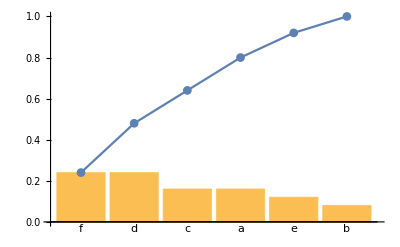

```mathematica
data=RandomChoice[CharacterRange["a","f"],{25}];
ParetoPlot[data]
```

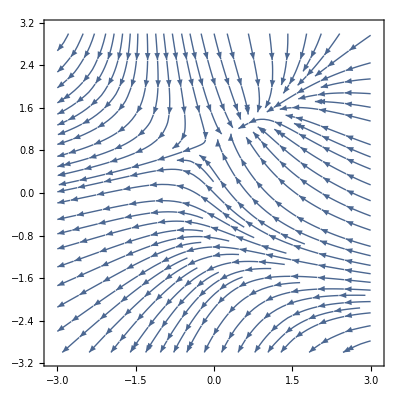

```mathematica
StreamPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3}]
```

```mathematica
StreamPlot[{{x,y},{y,-x}},{x,-3,3},{y,-3,3}]
```

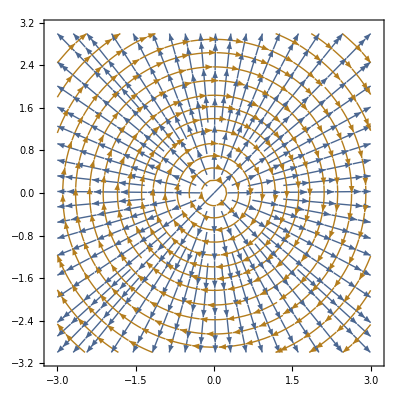

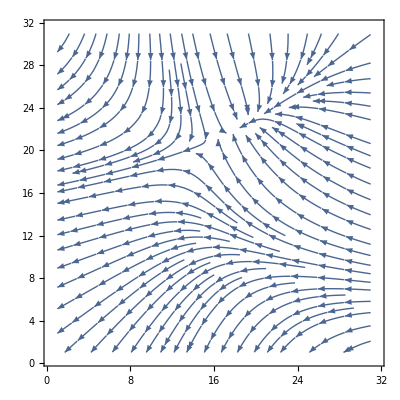

```mathematica
data=Table[{-1-x^2+y,1+x-y^2},{x,-3,3,.2},{y,-3,3,.2}];
ListStreamPlot[data]
```

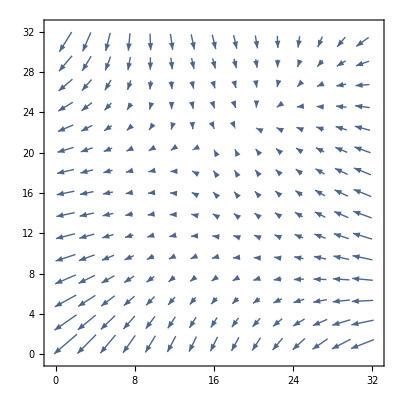

```mathematica
ListVectorPlot[data]
```

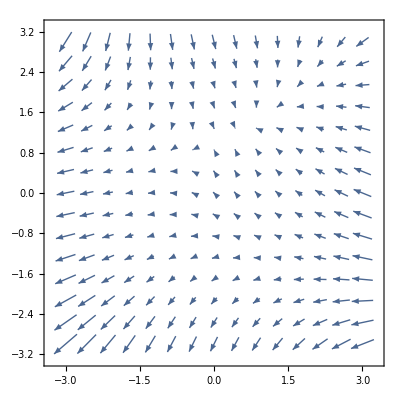

```mathematica
VectorPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3}]
```

```mathematica
VectorPlot3D[{x,y,z},{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
PieChart[{1,2,3,4,5}]
```

-Graphics-

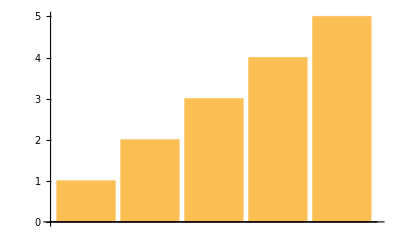

```mathematica
BarChart[{1,2,3,4,5}]
```

```mathematica
PieChart3D[{1,23,4,352,2,42}]
```

-Graphics3D-

```mathematica
BarChart3D[{1,124,2,2,2,1,1,2,42,4}]
```

-Graphics3D-

```mathematica
SectorChart[{{{1,1},{1,2},{1,3}},{{7,3},{5,2},{1,1}}}]
```

-Graphics-

```mathematica
GeoGraphics[GeoRange->"World",GeoProjection->"Robinson"]
```

-Graphics-

```mathematica
s=GeoGraphics[{GeoPosition[{{34,112},{45,123}}],GeoPosition[{{48,112},{53,123}}]},Axes->True]
```

-Graphics-

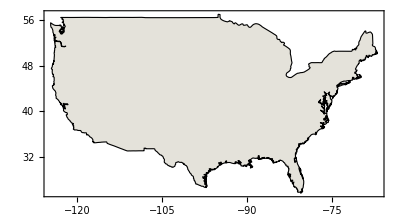

```mathematica
Show[CountryData["UnitedStates",{"Shape","Mercator"}],Frame->True]
```

```mathematica
GeoRegionValuePlot[{LinguisticAssistant->2,LinguisticAssistant->3,LinguisticAssistant->4,LinguisticAssistant->5,LinguisticAssistant->6,LinguisticAssistant->7}]
```

-Graphics-

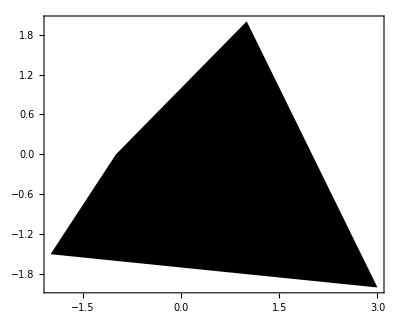

```mathematica
Graphics[Polygon[{{-1,0},{1,2},{3,-2},{-2,-1.5}}],Frame->True]
```

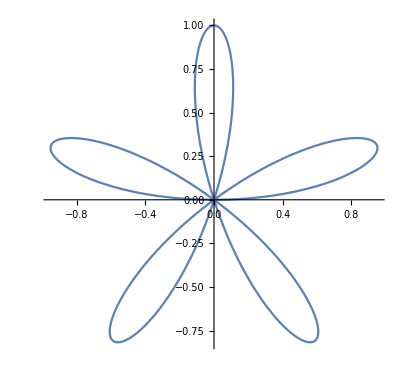

```mathematica
PolarPlot[Sin[5θ],{θ,0,π}]
```

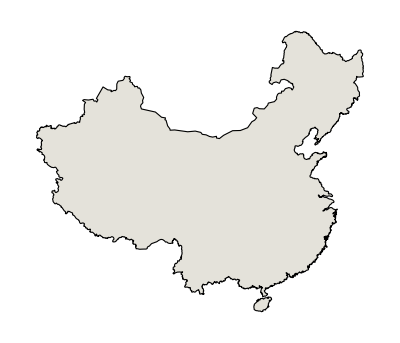

```mathematica
CountryData[LinguisticAssistant,"Shape"]
```

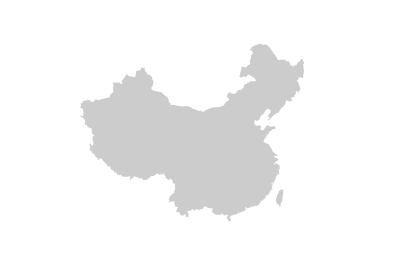

```mathematica
GeoGraphics[Polygon[{LinguisticAssistant,LinguisticAssistant}],GeoBackground->None]
```

```mathematica
x=Table[GeoPosition[{RandomReal[{-90,90}],RandomReal[{-180,180}]}],{i,200}];
GeoListPlot[x]
```

-Graphics-

```mathematica
GeoGraphics[Point[x]]
```

-Graphics-

```mathematica
data=DeleteCases[Reverse[CityData[#,"Coordinates"]]&/@CityData[{All,"India"}],Missing["NotAvailable"]];
Show[SmoothDensityHistogram[data,.3,ColorFunction->"SunsetColors",PlotPoints->150,Mesh->20,MeshStyle->Opacity[.1],PlotRange->All],Graphics[{FaceForm[],EdgeForm[Directive[White,Opacity[.7]]],CountryData["India","Polygon"]}]]
```

-Graphics-

```mathematica
a=SmoothDensityHistogram[data,.3,ColorFunction->"SunsetColors",PlotPoints->150,Mesh->100,MeshStyle->Opacity[.1],PlotRange->All]
```

-Graphics-

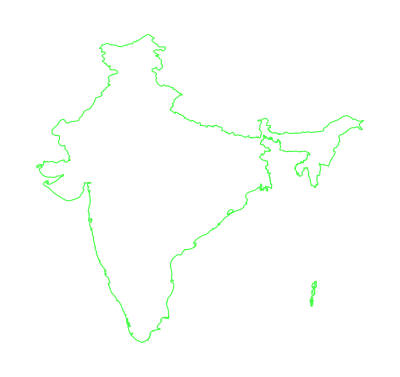

```mathematica
b=Graphics[{FaceForm[],EdgeForm[Directive[Green,Opacity[.7]]],CountryData["India","Polygon"]}]
```

```mathematica
Show[a,b]
```

-Graphics-

```mathematica
data
```

```mathematica
dd=Table[Append[data[[i]],RandomReal[{0,i}]],{i,Dimensions[data][[1]]}];
```

```mathematica
ListContourPlot[dd,Mesh->All]
```

-Graphics-

```mathematica
outlines=Table[DeleteCases[CountryData[r,"SchematicPolygon"],Polygon[_Missing]],{r,{"SouthAmerica","NorthAmerica","Africa","Europe","Asia","Australia"}}]
```

{1}
 |  |  |  |

```mathematica
ListDensityPlot[Reverse@data,ColorFunction->"DeepSeaColors",AspectRatio->Automatic,DataRange->{{-180,180},{-90,90}},Epilog->{FaceForm[],EdgeForm[Opacity[0.5]],outlines},PlotRange->{{-180,180},{-90,90}}]
```

-Graphics-

```mathematica
outlines
```